# Natural Language Processing

### Home-growing a parser

Fez Zaman — Wolfram|Alpha: Linguistics Curator
Jeremy Stratton-Smith — Wolfram|Alpha: Math Content Developer
7.2.2019

## Introductions:

# Outline/Agenda

Functions to know

What is natural language processing (NLP)?

Examples

How is it done?

1. Lexical Analysis

2. Syntactic Analysis

3. Semantic Analysis

Extensions and questions

## Functions to know

#### String functions:

StringSplit, StringJoin, StringReplace, StringJoin (<>), StringExpression (~~), EndOfString, WhitespaceCharacter, ToLowerCase

#### Patterns:

PatternSequence, Alternatives (|), _, __, ___, Repeated (..), PatternTest (?)

#### Boolean functions:

IntegerQ, NumberQ, NumericQ, MatchQ

#### Other:

Row, Style, ReplaceAll (/.), RuleDelayed (:>), Module, Block, With, IntegerDigits

## What is natural language processing?

```mathematica
Graph[{"natural \n language "-> "natural \n language \n processor","natural \n language \n processor"->"code"(*, "code"->"Output"*) }, $graphstyle]
```

-Graphics-

### Examples:

#### Interpreter, SemanticInterpretation, Wolfram | Alpha, Alexa, Siri, Google Home, etc.

### Examples:

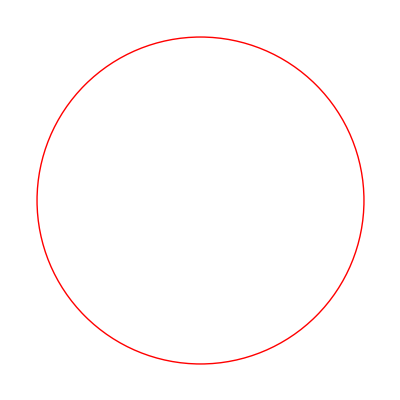

```mathematica
Interpreter["SemanticExpression"]["draw a red circle"]
```

what is the 400th most common female name

WolframAlphaQueryResults

# NLP Code In Action: Arithmetic

Our code only handles multiplication, division, addition and subtraction.

```mathematica
<<NLAUE`src`NLAUE`
```

```mathematica
NLAUE
```

## Loading steps:

Download NLAUE file into whatever folder you are keeping your WSC things in

Run <<(*path to file*)`NLAUE`in a fresh notebook

run NLAUE

Res: Jeremy

## How can it be done?

```mathematica
Graph[{"natural \n language"->"lexical \n analysis","lexical \n analysis"->"syntactic \n analysis","syntactic \n analysis"->"semantic \n analysis", "semantic \n analysis"->"code"(*,"code"->"output"*)},$graphstyle]
```

-Graphics-

### 1. Lexical analysis

What are the meaningful string of characters (tokens) in the input?

### 2. Syntactic analysis

What is the grammatical structure of the tokens we created?

### 3. Semantic analysis

Does the structure that we created make sense?

## 1. Lexical Analysis: Tokenization

#### Take input string and break it up into expressions recognized by the WL beyond simply being a string.

## 1.1 Break into words

### Ex. “what is two plus two?”

{"what", "is", “two”, “plus”, “two”, “?"}

### Ex. “myfavoriteflavoroficecreamismint”

{“my”, “favorite”, “flavor”, “of”, “ice”, “cream”, “is”, “mint”}

## 1.2 Desired tokens

Plus, Subtract, Times, Divide, Numbers, $Fluff

## 1.3 Tokenize relevant words into WL expressions

### Ex. “what is two plus two?”

{$Fluff, 2, Plus, 2, $Fluff}

### Ex. “what is two minus three times four?”

{$Fluff, 2, Subtract, 3, Times, 4, $Fluff}

## 1.4 Creating tokens

"what is two minus three times four?"

1.4.1: insert whitespace
	-> "what is two minus three times four ?"
	
1.4.2: split by whitespace (StringSplit[])
	-> {"what", "is", "two", "minus", "three", "times", "four", "?"}
	
1.4.3: convert number words to numbers
	-> {"what", "is", 2, "minus", 3, "times", 4, "?"}
	
1.4.4: convert operations to WL operation Heads
	-> {"what", "is", 2, Subtract, 3, Times, 4, "?"}

1.4.5: convert fluff to $Fluff
	-> {$Fluff, 2, Subtract, 3, Times, 4, $Fluff}

## 1.5 createTokens Code

```mathematica
textToNumbers[
	StringSplit[
		injectSpace["what is three minus four multiplied by 5?"]]]
```

```mathematica
{"what", "is", 3, "minus", 4,"multiplied", "by", 5, "?"}
```

Using ReplaceAll ( /. )

```mathematica
ReplaceAll[
	{"what", "is", 3, "minus", 4,"multiplied", "by", 5, "?"},
	("-"|"minus") -> Subtract
]
```

{what,is,3,Subtract,4,multiplied,by,5,?}

```mathematica
{"what", "is", 3, Subtract, 4, "multiplied", "by", 5, "?"}/.
	{a___, "multiplied", "by", b___} :> {a, Times, b}
```

{what,is,3,Subtract,4,Times,5,?}

```mathematica
{"what", "is", 3, Subtract, 4, Times, 5, "?"}/.{
	{a___, beginningfluffPatterns, b___} :> {a, $Fluff, b},
	{a___, endingfluffPatterns, b___} :> {a, $Fluff, b}}
```

```mathematica
{$Fluff,3,Subtract,4,Times,5,$Fluff}
```

```mathematica
createTokens[input_String] := Module[{tokenList = textToNumbers[StringSplit[injectSpace[input]]],
	beginningfluffPatterns =
		Alternatives[
			PatternSequence["what"|PatternSequence["how","much"], "is"|"does"],
			"what's",
			PatternSequence["tell","me","what"],
			""],
	endingfluffPatterns =
		Alternatives["is","equals"|"equal" | "?"],	
	ops},
	
	ops = {
		("+"|"plus") -> Plus,
		("-"|"minus") -> Subtract,
		{a___, "multiplied", "by", b___} :> {a, Times, b},
		("*"|"times") -> Times,
		{a___, "divided", "by", b___} :> {a, Divide, b},
		("/"|"÷") -> Divide,
		{a___, beginningfluffPatterns, b___} :> {a, $Fluff, b},
		{a___, endingfluffPatterns, b___} :>  {a, $Fluff, b}};
		
	tokenList //. ops
]
```

# 1. Lexical Analysis — 5 minutes

## Questions?

## What are other ways of asking “what is two plus two?”

### What do the fluff patterns look like for each of your answers to the above?

# Break/Question time

## 2. Syntactic Analysis/Parsing

What arrangement of tokens will be useful for arithmetic?

### {$Fluff, 2, Plus, 2, $Fluff}

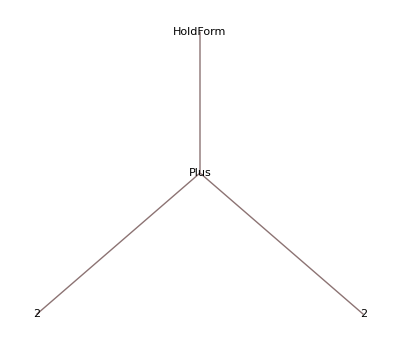

### {$Fluff, 2, Subtract, 3, Times, 4, $Fluff}

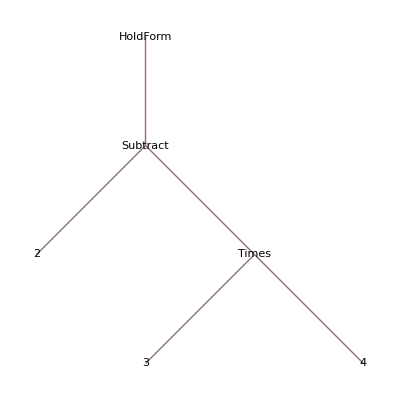

## 2.1 Grouping tokens

Building meaning by categorizing tokens or sequences of tokens.

### {$Fluff, 2, Plus, 2, $Fluff}

Goal: Plus[2,2]

### {$Fluff, 2, Subtract, 3, Times, 4, $Fluff}

Goal: Subtract[2,Times[3,4]]

## 2.2 Transformation rules

Rearranging the list of tokens we have into WL syntax and introducing appropriate order of operations

```mathematica
mathExpr =Alternatives[_?NumericQ, _List]
```

{$Fluff,   2,  Subtract, 3, Times, 4, $Fluff}

2.2.1: change Times/Divide between mathExprs to {head, opA, opB}
	-> {$Fluff, 2, Subtract, {Times, 3, 4}, $Fluff}
	
2.2.2: change Plus/Subtract between mathExprs to {head, expr1, expr2} 
	-> {$Fluff, {Subtract, 2, {Times, 3, 4}}, $Fluff}
	
2.2.3: de-fluff 
	-> {Subtract, 2, {Times, 3, 4}}

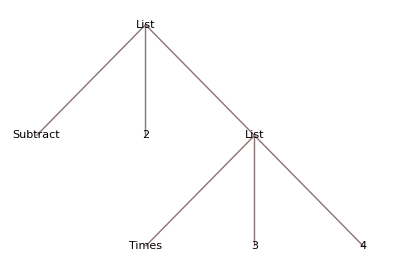

```mathematica
TreeForm[{Subtract, 2, {Times, 3, 4}}]
```

## 2.3 parseInput code

```mathematica
mathExpr =Alternatives[_?NumericQ, _List];
```

```mathematica
ReplaceAll[
	{$Fluff, 2, Subtract, 3, Times, 4, $Fluff},
	{start___, opa:mathExpr, head:(Times | Divide), opb:mathExpr, end___}:>
		{start, {head, opa, opb}, end}]
```

{$Fluff,2,Subtract,3,Times,4,$Fluff}

```mathematica
ReplaceAll[
	{$Fluff, 2, Subtract, {Times, 3, 4}, $Fluff},
	{start___, opa:mathExpr, head:(Plus | Subtract), opb:mathExpr, end___}:>
		{start, {head, opa, opb}, end}]
```

{$Fluff,2,Subtract,{Times,3,4},$Fluff}

```mathematica
parseInput[input_List]:=Module[
	{tokenList = input, mathExpr = Alternatives[_?NumericQ, _List]},

	(* Transformation rules *)
	tokenList = tokenList //. {
		{start___, "("|"[", opa:mathExpr, head_Symbol, opb:mathExpr, ")"|"]", end___}:>
			{start, {head, opa, opb}, end},
		{start___, opa:mathExpr, head:(Times | Divide), opb:mathExpr, end___}:>
			{start, {head, opa, opb}, end},
		{start___, opa:mathExpr, head:(Plus | Subtract), opb:mathExpr, end___}:>
			{start, {head, opa, opb}, end},
		{start___, opa:mathExpr, head_Symbol, opb:mathExpr, end___}:>
			{start, {head, opa, opb}, end}
	};
	
	(* de-fluffing *)
	tokenList = tokenList /. (Alternatives[
			{$Fluff, content_List, $Fluff},
			{$Fluff, content_List},
			{content_List, $Fluff}
		]):>content
]
```

## 2. Parser output — 5 minutes

### {$Fluff, 2, Plus, 2, $Fluff}

{Plus, 2, 2}

### {$Fluff, 2, Subtract, 3, Times, 4, $Fluff}

{Subtract, 2, {Times, 3, 4}}

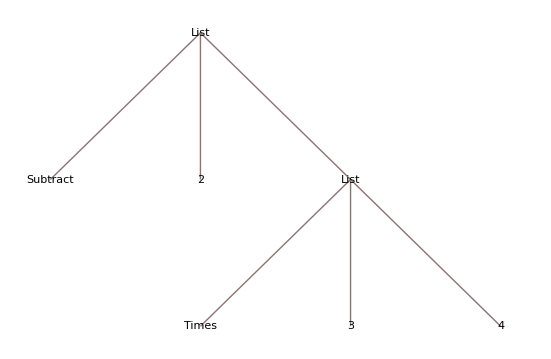
We now have: -Graphics-

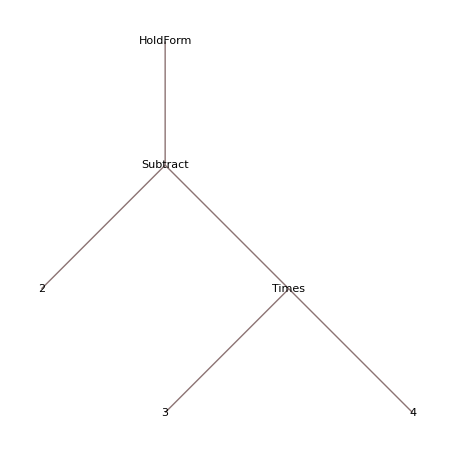
We want:-Graphics-

# Questions?

## 3. Semantic Analysis

Does the resulting parse make sense?

### {Subtract, 2, {Times, 3, 4}}

```mathematica
{head_, opa_?NumericQ, opb_?NumericQ} :> head[opa,opb]
```

expr /. List -> Construct

{Subtract, 2, {Times, 3, 4}}
	-> {Subtract, 2, Times[3, 4]}
	-> {Subtract, 2, 12}
	-> Subtract[2, 12]
	-> -10

Check – “is it a number?”

At this point, we have looked at a lot of code. Can anyone describe what this rule will accomplish towards our goal?

## 3.1 composeResult code

```mathematica
composeResult[input_String] := Module[{res, heldRes},
	res = createTokens[input];
	res = parseInput[res];
	
	(* de-nesting lists for display *)
	heldRes = res //. {head_, opa_, opb_} :> HoldForm[head[opa,opb]];
	
	(* recursively computing result *) 
	(* exercise: accomplish the below result using Construct *)
	res = res //. {head_, opa_?NumericQ, opb_?NumericQ} :> head[opa,opb];
	
	(* check semantics (does it make sense?) *)
	If[NumericQ[res],
		Row[{heldRes, "==", res}],
		Row[{Style["["<>input<>"]",15, FontColor->Blue],Style[" is not supported ",15, FontColor->Gray]}]]
]
```

```mathematica
{Subtract, 2, {Times, 3, 4}}//.
	{head_, opa_(*?NumericQ*), opb_(*?NumericQ*)} :> HoldForm[head[opa,opb]]
```

2-3 4

```mathematica
{Subtract, 2, {Times, 3, 4}}//.
	{head_, opa_?NumericQ, opb_?NumericQ} :> head[opa,opb]
```

-10

## Extensions

Deep Learning with Neural Networks

https://youtu.be/3KNVx1ciN_g?t=150

# Thank you!

#### Sources:

Aho, A. V., Sethi, R., and Ullman, J. D. 1985. Compilers: Principles, 	Techniques and Took. Addison-Wesley, Reading, Mass.

#### Style:

```mathematica
$graphstyle = Sequence[VertexLabels->Placed["Name",Center], ImageSize->1000, PlotTheme->"Business"];
```